```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2025-03-19-17-29-37.json"];
raw=Association[#]&/@raw;

raw[[1]]
```

<|solSet→-0.37,gridCount→16.,norm_emit_x→0.0000104137,norm_emit_y→0.0000103975,norm_emit_x_90→6.001×10^-6,norm_emit_y_90→5.9905×10^-6,emitSI90_x→8.7298×10^-6,emitSI90_y→8.8942×10^-6|>

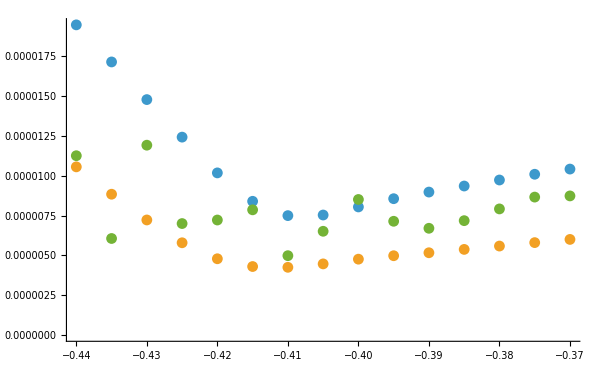

```mathematica
ListPlot[{
{#solSet,#["norm_emit_x"]}&/@raw,
{#solSet,#["norm_emit_x_90"]}&/@raw,
{#solSet,#["emitSI90_x"]}&/@raw
}
]
```

## With phase scan

```mathematica
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2025-03-19-17-59-20.json"];*)
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2025-03-20-11-27-44.json"];

raw=Association[#]&/@raw;
```

```mathematica
raw[[1]]
```

<|L0APhaseOffset→-15.,solSet→-0.39,impactGridCount→64.,norm_emit_x→4.2667×10^-6,norm_emit_y→4.2755×10^-6,norm_emit_x_90→1.7419×10^-6,norm_emit_y_90→1.7492×10^-6,emitSI90_x→2.8325×10^-6,emitSI90_y→2.8151×10^-6|>

```mathematica
ListDensityPlot[
{#solSet,#L0APhaseOffset,10^6#["norm_emit_x_90"]}&/@raw,
ColorFunction->"Rainbow",
InterpolationOrder->0,
PlotLegends->Automatic,
Mesh->All,
ImageSize->800,
FrameLabel->{"Solenoid setting [kG-m]","L0A phase [°]"},
PlotLabel->"L0AFEND normalized emittance [μm-rad]",
LabelStyle->20
]
```

-Graphics-

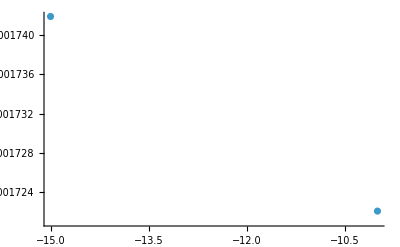

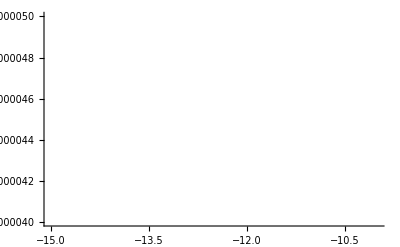

```mathematica
ListPlot[{#L0APhaseOffset,#["norm_emit_x_90"]}&/@raw]
ListPlot[{#L0APhaseOffset,#["norm_emit_x_90"]}&/@raw,PlotRange->{4*^-6,5*^-6}]
```